```mathematica
R=3;
Plot3D[Sqrt[x^2+y^2],{x,-R,R},{y,-R,R},
RegionFunction->Function[{x,y},x^2+y^2<R],Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Plot3D[√(x^2+y^2),{x,-R,R},{y,-R,R},Mesh->Automatic,MeshFunctions->Automatic,RegionFunction->Function[{x,y},x^2+y^2<R],Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Plot3D[{√(x^2+y^2),1},{x,-R,R},{y,-R,R},Mesh->None,Mesh->Automatic,MeshFunctions->Automatic,RegionFunction->Function[{x,y},x^2+y^2<R],Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Plot3D[{√(x^2+y^2),1},{x,-R,R},{y,-R,R},PlotTheme->"Scientific",Mesh->None,Mesh->Automatic,MeshFunctions->Automatic,RegionFunction->Function[{x,y},x^2+y^2<R],Boxed->False,Axes->False,PlotStyle->{Opacity[0.5],Opacity[0.7]}]
```

-Graphics3D-

```mathematica
cone=Plot3D[√(x^2+y^2),{x,-R,R},{y,-R,R},PlotTheme->"Scientific",Mesh->None,Mesh->Automatic,MeshFunctions->Automatic,
BoxRatios->Automatic,
RegionFunction->Function[{x,y},x^2+y^2<R^2],Boxed->False,Axes->False,PlotStyle->{Opacity[0.5],PlotRange->{0,R}}
]
```

-Graphics3D-

```mathematica
plane=Plot3D[x/2+y/3+1,{x,-R,R},{y,-R,R},PlotTheme->"Classic",Mesh->None,Mesh->Automatic,MeshFunctions->Automatic,Boxed->False,Axes->False,PlotStyle->{Opacity[0.7]}]
```

-Graphics3D-

```mathematica
Show[cone,plane]
```

-Graphics3D-

```mathematica
circle=ParametricPlot3D[{2Cos[t],2Sin[t],2},{t,0,2π},
PlotStyle->RGBColor[1, 1, 0]
]
```

-Graphics3D-

```mathematica
Show[cone,plane,circle]
```

-Graphics3D-

```mathematica
Export["/home/pewhite/github/aos/aos-10/conics/fig-circle-cone.pdf",%70,"PDF"]
```

/home/pewhite/github/aos/aos-10/conics/fig-circle-cone.pdf

```mathematica
Plot[x^2+y^2==1,{x,-1,1},{y,-1,1}]
```

Plot::nonopt: Options expected (instead of {y,-1,1}) beyond position 2 in Plot[x^2+y^2==1,{x,-1,1},{y,-1,1}]. An option must be a rule or a list of rules.

Plot[x^2+y^2==1,{x,-1,1},{y,-1,1}]

plot x^2+y^2==1

WolframAlphaQueryResults

```mathematica
WolframAlpha["plot x^2/4+y^2/9==1",{{"ImplicitPlot",1},"Input"}]
```

Missing[NotAvailable]

```mathematica
ImplicitPlot[x^2+y^2==1]
```

ImplicitPlot[x^2+y^2==1]

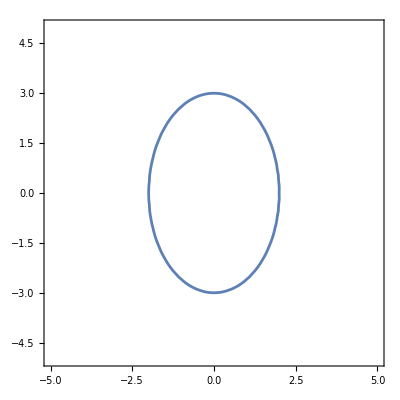

```mathematica
h=0;
k=0;
a=2;
b=3;
ContourPlot[(x-h)^2/a^2+(y-k)^2/b^2==1,{x,-5,5},{y,-5,5},Axes->True]
```

```mathematica
Range[-10,10]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

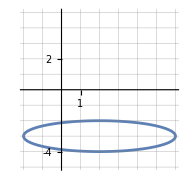

```mathematica
h=2;k=-3;a=4;b=1;
ContourPlot[(x-h)^2/a^2+(y-k)^2/b^2==1,{x,-2,6},{y,-5,5},Axes->True,Frame->None,Ticks->{Range[-10,10]},GridLines->{Range[-10,10]}]
```

```mathematica
f[h_,k_,a_,b_]:=ContourPlot[(x-h)^2/a^2+(y-k)^2/b^2==1,{x,-3,7},{y,-5,5},Axes->True,Frame->None,Ticks->{Range[-9,9,2]},GridLines->{Range[-10,10]},ImageSize->Small,ImagePadding->None]
```

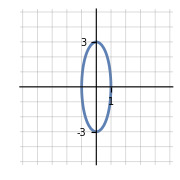

```mathematica
f[0,0,1,3]
```

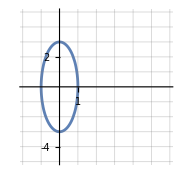

```mathematica
Show[%116,ImageSize->Small]
```

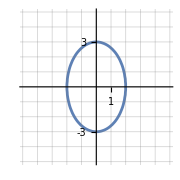

```mathematica
f[0,0,2,3]
```

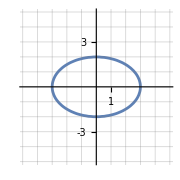

```mathematica
f[0,0,3,2]
```

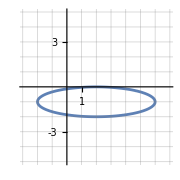

```mathematica
f[2,-1,4,1]
```

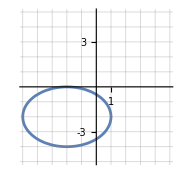

```mathematica
f[-2,-2,3,2]
```